```mathematica
With[
{base="C",colofour="colofour"},
With[{keys=supertemp2},
Fold[And,Table[
Fold[Or,Table[(var/.RepGraph4)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
]//Reduce
```

(-Graphics-6971>1&&-Graphics-6371>1&&-Graphics-4731>1&&-Graphics-3771>1&&-Graphics-3640>0)||(-Graphics-6971>1&&-Graphics-4731>1&&-Graphics-6071>1&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3670>0&&-Graphics-3651>1)||(-Graphics-6971>1&&-Graphics-4731>1&&-Graphics-3670>0&&-Graphics-3640>0)||(-Graphics-6371>1&&-Graphics-3771>1&&-Graphics-6071>1&&-Graphics-4450>0&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3651>1)||(-Graphics-6371>1&&-Graphics-3771>1&&-Graphics-4450>0&&-Graphics-3640>0)||(-Graphics-4480>0&&-Graphics-6071>1&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3651>1)||(-Graphics-4480>0&&-Graphics-3640>0)||(-Graphics-4450>0&&-Graphics-3670>0)

```mathematica
TableForm[

Sort[ExpressionToList[
BooleanConvert[(With[
{base="C",colofour="colofour"},
With[{keys=supertemp2},
Fold[And,Table[allGraphs4[atom,"colofour"]>0,{atom,Select[allGraphs4AtomKeys,allGraphs4[#,"comp"]===Greater&]}]]&&
Fold[And,Table[
Fold[Or,Table[(var)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
])/.RepGraph4,"DNF"]
],Length[#1]<Length[#2]&]
]
```

-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-6071>0&&-Graphics-4450>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3670>0&&-Graphics-3651>0
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-4480>0&&-Graphics-6071>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3651>0&&-Graphics-3640>0
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6371>1&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-3771>1&&-Graphics-6071>0&&-Graphics-4450>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3651>0&&-Graphics-3640>0
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6971>1&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4731>1&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-6071>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3670>0&&-Graphics-3651>0&&-Graphics-3640>0
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-4480>0&&-Graphics-6071>0&&-Graphics-6071>1&&-Graphics-3731>0&&-Graphics-3731>1&&-Graphics-3911>0&&-Graphics-3911>1&&-Graphics-3651>0&&-Graphics-3651>1
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6971>1&&-Graphics-6371>0&&-Graphics-6371>1&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4731>1&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-3771>1&&-Graphics-6071>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3651>0&&-Graphics-3640>0
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6371>1&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-3771>1&&-Graphics-6071>0&&-Graphics-6071>1&&-Graphics-4450>0&&-Graphics-3731>0&&-Graphics-3731>1&&-Graphics-3911>0&&-Graphics-3911>1&&-Graphics-3651>0&&-Graphics-3651>1
-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6971>1&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4731>1&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-6071>0&&-Graphics-6071>1&&-Graphics-3731>0&&-Graphics-3731>1&&-Graphics-3911>0&&-Graphics-3911>1&&-Graphics-3670>0&&-Graphics-3651>0&&-Graphics-3651>1

```mathematica
TableForm[

Sort[ExpressionToList[
BooleanConvert[(With[
{base="C",colofour="colofour"},
With[{keys=supertemp2},
Fold[And,Table[
Fold[Or,Table[(var)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
])/.RepGraph4,"DNF"]
],Length[#1]<Length[#2]&]
]
```

-Graphics-4450>0&&-Graphics-3670>0
-Graphics-4480>0&&-Graphics-3640>0
-Graphics-6371>1&&-Graphics-3771>1&&-Graphics-4450>0&&-Graphics-3640>0
-Graphics-6971>1&&-Graphics-4731>1&&-Graphics-3670>0&&-Graphics-3640>0
-Graphics-4480>0&&-Graphics-6071>1&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3651>1
-Graphics-6971>1&&-Graphics-6371>1&&-Graphics-4731>1&&-Graphics-3771>1&&-Graphics-3640>0
-Graphics-6371>1&&-Graphics-3771>1&&-Graphics-6071>1&&-Graphics-4450>0&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3651>1
-Graphics-6971>1&&-Graphics-4731>1&&-Graphics-6071>1&&-Graphics-3731>1&&-Graphics-3911>1&&-Graphics-3670>0&&-Graphics-3651>1

```mathematica
supertemp2
```

{0,243,324,351,360,352,333,334,325,414,270,279,282,280,273,274,276,271,252,255,256,253,246,247,244,81,108,117,118,109,90,91,82,162,190,27,36,39,40,37,30,31,28,9,12,13,16,10,3,4,6,1}

```mathematica
k3=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs4],(allGraphs4[#,"atleast"]≠ (allGraphs4[#,colofour]/.RepAtLeast4[base]))&]
]
```

{0,243,324,351,360,361,352,333,334,325,414,442,270,279,282,283,286,280,273,274,276,271,252,255,256,253,246,247,244,81,108,117,118,109,90,91,82,162,190,27,36,39,40,37,30,31,28,9,12,13,16,10,3,4,6,1}

```mathematica
Sort[k3]//Length
```

56

```mathematica
Sort[supertemp2]//Length
```

52

```mathematica
TableForm[

Sort[ExpressionToList[
BooleanConvert[(With[
{base="C",colofour="colofour"},
With[{keys=Select[Keys[allGraphs4],(allGraphs4[#,"atleast"]≠ (allGraphs4[#,colofour]/.RepAtLeast4[base]))&]},
Fold[And,Table[
Fold[Or,Table[(var)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
])/.RepGraph4,"ESOP"]
],Length[#1]<Length[#2]&]
]
```

-Graphics-4450>0&&-Graphics-3670>0
-Graphics-4480>0&&-Graphics-3670≤0&&-Graphics-3640>0
-Graphics-4480>0&&-Graphics-4450≤0&&-Graphics-3670>0&&-Graphics-3640>0

```mathematica
BooleanConvert[(With[
{base="C",colofour="colofour"},
With[{keys=Select[Keys[allGraphs4],(allGraphs4[#,"atleast"]≠ (allGraphs4[#,colofour]/.RepAtLeast4[base]))&]},Fold[And,Table[allGraphs4[atom,"colofour"]>0,{atom,Select[allGraphs4AtomKeys,allGraphs4[#,"comp"]===Greater&]}]]&&
Fold[And,Table[
Fold[Or,Table[(var)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
])/.RepGraph4,"DNF"]
```

(-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-4480>0&&-Graphics-6071>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3651>0&&-Graphics-3640>0)||(-Graphics-7281>0&&-Graphics-6971>0&&-Graphics-6371>0&&-Graphics-6081>0&&-Graphics-4731>0&&-Graphics-4001>0&&-Graphics-3771>0&&-Graphics-6071>0&&-Graphics-4450>0&&-Graphics-3731>0&&-Graphics-3911>0&&-Graphics-3670>0&&-Graphics-3651>0)

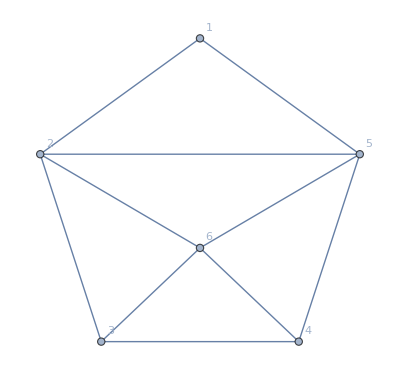

```mathematica
Graph[EdgeAdd[CycleGraph[5],{2<->6,3<->6,4<->6,5<->6,5<->2}],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
Map[With[{g=SetsToCompleteGraph[SymbolToSets[#]]},Labeled[g,Style[SymbolToLabel[#],If[PlanarGraphQ[g],Blue,Red]]]]&, FindFullFormula[EdgeAdd[CycleGraph[5],{2<->6,3<->6,4<->6,5<->6,5<->2}]]]
```

{-Graphics-1♁2♁3♁4♁5♁6,-Graphics-1♁2♁35♁4♁6,-Graphics-1♁24♁3♁5♁6,-Graphics-1♁24♁35♁6,-Graphics-16♁2♁3♁4♁5,-Graphics-16♁2♁35♁4,-Graphics-16♁24♁3♁5,-Graphics-16♁24♁35,-Graphics-14♁2♁3♁5♁6,-Graphics-14♁2♁35♁6,-Graphics-13♁2♁4♁5♁6,-Graphics-13♁24♁5♁6}

```mathematica
BooleanConvert[(With[
{base="C",colofour="colofour"},
With[{keys=Select[Keys[allGraphs4],(allGraphs4[#,"atleast"]≠ (allGraphs4[#,colofour]/.RepAtLeast4[base]))&]},
Fold[And,Table[
Fold[Or,Table[(var)>(var/.RepAtLeast4[base]),{var,ListofVars[(allGraphs4[k,colofour])]}]],
{k,keys}
]
]
]
])/.RepGraph4,"DNF"]
```

(-Graphics-4480>0&&-Graphics-3640>0)||(-Graphics-4450>0&&-Graphics-3670>0)